```mathematica
res = 40;
kmomx = Subdivide[-π,π,res];
kmomy = Drop[Subdivide[-π,π,res],-1];
m = 0.5;

Xi={PauliMatrix[0],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
X[Mu_]:=Xi[[Mu+1]]

Hc[{kx_,ky_}]:= N[Sin[kx]X[1]+Sin[ky]X[2]+(m-2+Cos[kx]+Cos[ky])X[3]];

HcOBC[{kx_,y_}]:= Sum[1/res N[Sin[kx]X[1]+Sin[ky]X[2]+(m-2+Cos[kx]+Cos[ky])X[3]]Exp[ⅈ ky y],{ky,kmomy}];

HcOBCMatrix[kx_]:=ArrayFlatten[Table[Which[xpos==ypos,HcOBC[{kx,0}],xpos==ypos+1,HcOBC[{kx,1}],xpos==ypos-1,HcOBC[{kx,-1}],True,0],{xpos,1,res},{ypos,1,res}]];
```

```mathematica
eigenvals = ParallelTable[SortBy[Eigenvalues[Hc[{kx,ky}]],Re],{kx,kmomx},{ky,kmomy}];

eigenvalsOBC = ParallelTable[SortBy[Eigenvalues[HcOBCMatrix[kx]],Re],{kx,kmomx}];
```

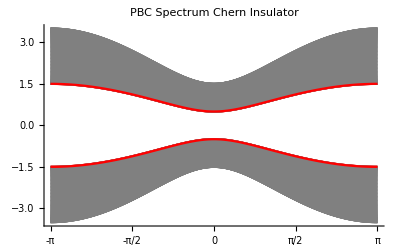
-Graphics-Momentum along one Direction k_1Hamiltonian Eigenvalues E_n

```mathematica
{nx,ny,nz}=Dimensions[eigenvals];

plotColors = Table[If[ky==res/2 || ky== res/2+1,Red,Gray],{ky,1,ny}];

ticks = {-π,-π/2,0,π/2,π};

ticksX = Table[If[t!=π,{Position[kmomx,x_/;x==t][[1,1]],ToString[StandardForm[t]]},{Length[kmomx],ToString[StandardForm[π]]}],{t,ticks}];

plots=Table[ListLinePlot[Transpose[eigenvals[[All,ky,All]]],PlotStyle->plotColors[[ky]],ImageSize->400,AxesOrigin->{-3,0},Ticks->{ticksX,Automatic},PlotRange->All,PlotLabel->"PBC Spectrum Chern Insulator"],{ky,ny}];

combinedPlot=Labeled[Show[{plots,plots[[res/2]]},PlotRange->All,PlotRangePadding->Scaled[0.05]],{"Momentum along one Direction \!\(\*SubscriptBox[\(k\), \(1 \)]\)","Hamiltonian Eigenvalues \!\(\*SubscriptBox[\(E\), \(n\)]\)"},{Bottom,Left},RotateLabel->True]
```

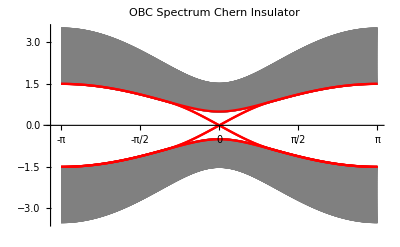
-Graphics-Momentum along one Direction k_1Hamiltonian Eigenvalues E_n

```mathematica
{nxO,nyO}=Dimensions[eigenvalsOBC];

plotColorsOBC = Table[If[ky==res-1 ||ky==res || ky== res+1||ky==res+2 ,Red,Gray],{ky,1,nyO}];

OBCPlot = ListLinePlot[Transpose[eigenvalsOBC],PlotStyle->plotColorsOBC,ImageSize->400,AxesOrigin->{-3,0},Ticks->{ticksX,Automatic},PlotRange->All,PlotLabel->"OBC Spectrum Chern Insulator"];

OBCPlotTop = ListLinePlot[Transpose[eigenvalsOBC[[;;,res-1;;res+2]]],PlotStyle->Red,ImageSize->400,AxesOrigin->{-1,0},Ticks->{ticksX,Automatic},PlotRange->All,PlotLabel->"OBC Spectrum Chern Insulator"];

Labeled[Show[OBCPlot,OBCPlotTop],{"Momentum along one Direction \!\(\*SubscriptBox[\(k\), \(1 \)]\)","Hamiltonian Eigenvalues \!\(\*SubscriptBox[\(E\), \(n\)]\)"},{Bottom,Left},RotateLabel->True]
```

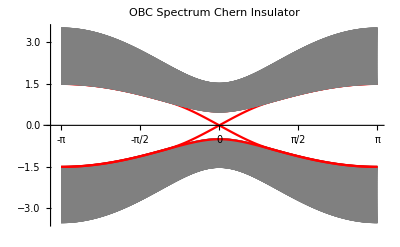

```mathematica
GraphicsGrid[{{combinedPlot,OBCPlot}},ImageSize->950]
```